```mathematica
GeneralLinearAnizatropy[α0_,U0_,χ0_,θ0_,β0_,P0_]:= 
Module[{α=α0,U=U0,χ=χ0,θ=θ0,β=β0,P=P0},
(*α - dissipation, α=ν/ω, ω->ω(1+ⅈα)*)
(*U - anizatropy: p^2=4πe^2*n/m, b=eB/(mc), v=p^2/ω^2, u=b^2/ω^2, and with dissipation: v->v(1-ⅈα), u->U(1-ⅈα)*)
(*χ - dimensionless wave vector magnitude; χ=Subscript[k, 0] L, and L=1*) 
(*θ - angel between wave vector and XOZ*)
(*β - angle between wave vector and magnetic field direction*)
(*P - wave polarisation; 2d-vector*)

(*=====================================================================================================================*)

(*Plasma configuration*)
X=3;(*plasma boundary*)
Δ=0.01;(*smoothing width, in parts of plasma whight*)
n=1/Δ; smoothingFunc=Function[x,(1+(x/X)^(2n))^-1]; v=Function[x,((X^2-x^2)/(X^2-1))*smoothingFunc[x]*(1-ⅈ*α)]; u=U(1-ⅈ*α);
Eps=({{1-v[x]/(1-u), ⅈ(√u)/(1-u)v[x], 0}, {-ⅈ(√u)/(1-u)v[x], 1-v[x]/(1-u), 0}, {0, 0, 1-v[x]}}); (*({{1-v[x]/(1-u), ⅈ(√u)/(1-u)v[x], 0}, {-ⅈ(√u)/(1-u)v[x], 1-v[x]/(1-u), 0}, {0, 0, 1-v[x]}})*)

(*=====================================================================================================================*)

(*Wave configuration*)
A=1;(*wave magnitude*)
k=χ({{Cos[θ]Sin[β]}, {Sin[θ]}, {Cos[θ]Cos[β]}})ᵀ[[1]];(*wave vector*)
Ε=A/Norm[P]({{Cos[β], -Sin[θ]Sin[β]}, {0, Cos[θ]}, {-Sin[β], -Sin[θ]Cos[β]}}).P; (*Electric field (!!!ESCAPE_SEQUENCE!!!)*)
Β=(k×Ε)/χ;(*Magnetic field (!!!ESCAPE_SEQUENCE!!!)*)

(*=====================================================================================================================*)

(*Maxwell equations*)
GeneralSystem = {
(*Ex[x]*Eps[x][[1,1]]+Ey[x]*Eps[x][[1,2]]==kz*By[x]-ky*Bz[x], Bx[x]==ky*Ez[x]-kz*Ey[x],*)
Ey'[x]==ⅈ*χ*(ky*(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]+Bz[x]),(*Ey'[x]==ⅈ*χ*(ky*Ex[x]+Bz[x])*)
Ez'[x]==ⅈ*χ*(kz*(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]-By[x]),(*Ez'[x]==ⅈ*χ*(kz*Ex[x]-By[x])*)
By'[x]==ⅈ*χ*(ky*(ky*Ez[x]-kz*Ey[x])-Eps[[3,3]]*Ez[x]),(*By'[x]==ⅈ*χ*(ky*Bx[x]-Eps[x][[3,3]]*Ez[x])*)
Bz'[x]==ⅈ*χ*(kz*(ky*Ez[x]-kz*Ey[x])+Eps[[2,1]]*(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]+Eps[[2,2]]*Ey[x])(*Bz'[x]==ⅈ*χ*(kz*Bx[x]+Eps[x][[2,1]]*Ex[x]+Eps[x][[2,2]]*Ey[x])*)
}/.{kx->k[[1]]/χ,ky->k[[2]]/χ,kz->k[[3]]/χ};

GeneralInitials = {Ey[2X]==Ε[[2]],Ez[2X]==Ε[[3]],By[2X]==Β[[2]],Bz[2X]==Β[[3]]};
Sol=NDSolveValue[{GeneralSystem,GeneralInitials},{Ey,Ez,By,Bz},{x,-2X,2X}];

(*=====================================================================================================================*)

(*Polarisation rotations*)
$Transmitted=If[P[[1]]==0,Conjugate[P[[2]]]/Abs[P[[2]]],Conjugate[P[[1]]]/Abs[P[[1]]]]({{P[[1]]/Norm[P]}, {P[[2]]/Norm[P]}})ᵀ[[1]];(*Transmitted wave*)
$IW=(({{Cos[β], 0, -Sin[β]}, {-Sin[β]Sin[θ], Cos[θ], -Cos[β]Sin[θ]}}).({{(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]}, {Ey[x]}, {Ez[x]}}))ᵀ[[1]]/.{kx->k[[1]]/χ,ky->k[[2]]/χ,kz->k[[3]]/χ,Ey[x]->Sol[[1]][x],Ez[x]->Sol[[2]][x],By[x]->Sol[[3]][x],Bz[x]->Sol[[4]][x]};
$IP=({{a/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==$IW[[1]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[$IW[[1]],x]/.x->(-2X)},{a,b}][[1]]}, {a/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==$IW[[2]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[$IW[[2]],x]/.x->(-2X)},{a,b}][[1]]}})ᵀ[[1]];
$Initial=If[$IP[[1]]==0,Conjugate[$IP[[2]]]/Abs[$IP[[2]]],Conjugate[$IP[[1]]]/Abs[$IP[[1]]]]({{($IP[[1]])/Norm[$IP]}, {($IP[[2]])/Norm[$IP]}})ᵀ[[1]];(*Initial wave*)
$RW=(({{Cos[π-β], 0, -Sin[π-β]}, {-Sin[π-β]Sin[-θ], Cos[-θ], -Cos[π-β]Sin[-θ]}}).({{(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]}, {Ey[x]}, {Ez[x]}}))ᵀ[[1]]/.{kx->k[[1]]/χ,ky->k[[2]]/χ,kz->k[[3]]/χ,Ey[x]->Sol[[1]][x],Ez[x]->Sol[[2]][x],By[x]->Sol[[3]][x],Bz[x]->Sol[[4]][x]};
$RP=({{b/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==$RW[[1]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[$RW[[1]],x]/.x->(-2X)},{a,b}][[1]]}, {b/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==$RW[[2]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[$RW[[2]],x]/.x->(-2X)},{a,b}][[1]]}})ᵀ[[1]];
$Reflected=If[$RP[[1]]==0,Conjugate[$RP[[2]]]/Abs[$RP[[2]]],Conjugate[$RP[[1]]]/Abs[$RP[[1]]]]({{($RP[[1]])/Norm[$RP]}, {($RP[[2]])/Norm[$RP]}})ᵀ[[1]];(*Reflected wave*)
(*Dissipation*)
$Dissipation=1-Norm[{$RP[[1]],$RP[[2]],0}×({0,0,1}×{$RP[[1]],$RP[[2]],0})]/Norm[{$IP[[1]],$IP[[2]],0}×({0,0,1}×{$IP[[1]],$IP[[2]],0})];

(*=====================================================================================================================*)

{Eps,k,Sol,$Initial,$Reflected,$Transmitted,$Dissipation}
]
```

NDSolveValue::precw: The precision of the differential equation ({SuperscriptBox[{}{}{}{}) is less than WorkingPrecision (50.).

NDSolveValue::nderr: Error test failure at x == 1.0024782294406065992208003861934921941020840017605; unable to continue.

InterpolatingFunction::dmval: Input value {-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-5.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

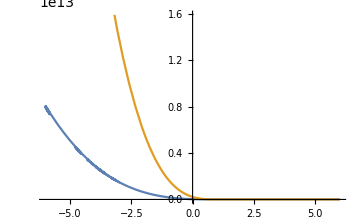
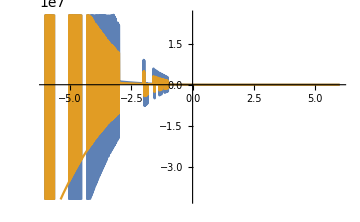
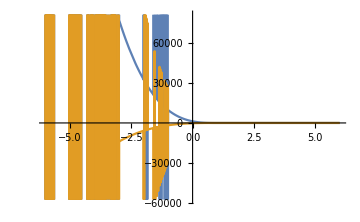
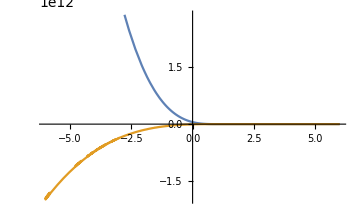

1.15329×10^-6

```mathematica
χ=20;β=0.18;δ=0.27;θ=π/4;ϕ=π/2;
sol=GeneralLinearAnizatropy[10^-5,(β*χ^(-2/3))^2,χ,ArcSin[δ*χ^(-1/3)],π/2,{Cos[θ],Sin[θ] ⅇ^(ⅈ ϕ)}];
Table[Plot[{Re[sol⟦3,i⟧[x]],Im[sol⟦3,i⟧[x]]},{x,-2X,2X},ImageSize->Medium],{i,1,4}]
sol[[7]]
```

```mathematica
SaveData[outputFile_,data_,format_]:= 
Module[{$outputFile=outputFile,$data=data,$format=format},
output=FileNameJoin[{NotebookDirectory[],$outputFile}];
destenationDirectory=DirectoryName[output];
If[DirectoryQ[destenationDirectory],,CreateDirectory[destenationDirectory]];
Export[output,$data,$format]
]
```

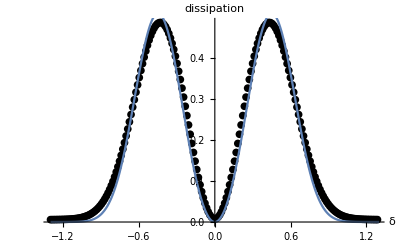

/Users/akutlin/Documents/private/VSHOPF/Egor/workspace/wolfram/results/isotropism/isotropism.csv

/Users/akutlin/Documents/private/VSHOPF/Egor/workspace/wolfram/results/isotropism/isotropism.pdf

```mathematica
(*Isotropic dimensionless dissipation; δ == Subscript[χ, 0]^(1/3)Sin[θ] == (Subscript[k, 0] L)^(1/3)*Sin[θ]*)
δDissipation={};
χ=100;
δbegining=-1.3;δend=1.3;δnstep=200;
ProgressIndicator[Dynamic[(δ-δbegining)/(δend-δbegining)]]
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,
δDissipation=Append[δDissipation,{δ,GeneralLinearAnizatropy[10^-5,0,χ,ArcSin[δ*χ^(-1/3)],π/2,{0,1}][[7]]}];
];
Clear[δ];

experiment=ListPlot[δDissipation,PlotRange->Full,AxesLabel->{δ,dissipation},PlotStyle->Black];
fittingFunction=Function[δ,a*δ^2 *Exp[-b*Abs[δ]^3 ]];
fit=FindFit[δDissipation,fittingFunction[δ],{a,b},δ];
theory=Plot[fittingFunction[δ]/.fit,{δ,δbegining,δend},PlotRange->Full,PlotLegends->ToString[fittingFunction[δ]/.fit,TraditionalForm]];

result=Show[{experiment,theory}]

SaveData["results/isotropism/isotropism.csv",δDissipation,"CSV"]
SaveData["results/isotropism/isotropism.pdf",result,"PDF"]
```

-Graphics3D-

/Users/akutlin/Documents/private/VSHOPF/Egor/workspace/wolfram/results/anisotropism/0.5pi_{0,1}/anisotropism.csv

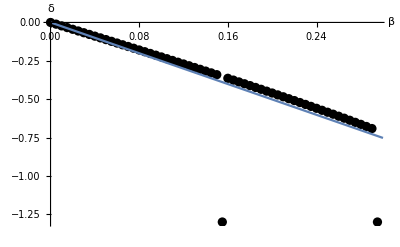

/Users/akutlin/Documents/private/VSHOPF/Egor/workspace/wolfram/results/anisotropism/0.5pi_{0,1}/zeroDissipationFromAnisortopism.csv

/Users/akutlin/Documents/private/VSHOPF/Egor/workspace/wolfram/results/anisotropism/0.5pi_{0,1}/zeroDissipationFromAnisortopism.pdf

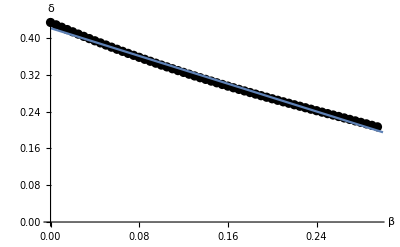

/Users/akutlin/Documents/private/VSHOPF/Egor/workspace/wolfram/results/anisotropism/0.5pi_{0,1}/maxDissipationFromAnisortopism.csv

/Users/akutlin/Documents/private/VSHOPF/Egor/workspace/wolfram/results/anisotropism/0.5pi_{0,1}/maxDissipationFromAnisortopism.pdf

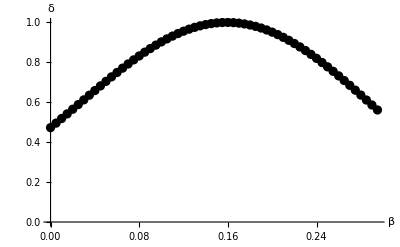

/Users/akutlin/Documents/private/VSHOPF/Egor/workspace/wolfram/results/anisotropism/0.5pi_{0,1}/maxValueDissipationFromAnisortopism.csv

/Users/akutlin/Documents/private/VSHOPF/Egor/workspace/wolfram/results/anisotropism/0.5pi_{0,1}/maxValueDissipationFromAnisortopism.pdf

```mathematica
(*Anisotropic dimensionless dissipation for TM-wave; δ == Subscript[χ, 0]^(1/3)Sin[θ] == (Subscript[k, 0] L)^(1/3)*Sin[θ], β == Subscript[χ, 0]^(2/3)√u*)
δβDissipation={};
χ=30;
δbegining=-1.3;δend=1.3;δnstep=100;
βbegining =0; βend = 0.5; βnstep = 100;
ProgressIndicator[Dynamic[(β-βbegining)/(βend-βbegining)+((βend-βbegining)/βnstep)*(δ-δbegining)/(δend-δbegining)]]
For[β=βbegining,β<βend,β+=(βend-βbegining)/βnstep,
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,
δβDissipation=Append[δβDissipation,{δ,β,GeneralLinearAnizatropy[10^-5,(β*χ^(-2/3))^2,χ,ArcSin[δ*χ^(-1/3)],π/2,{0,1}][[7]]}];
];
];
Clear[δ,β];

experiment=ListPlot3D[δβDissipation,PlotRange->Full,AxesLabel->{δ,β,dissipation}];
result=Show[{experiment}]

SaveData["results/anisotropism/0.5pi_{0,1}/anisotropism.csv",δβDissipation,"CSV"]
(*SaveData["results/anisotropism/0.5pi_{0,1}/anisotropism.pdf",result,"PDF"]*)

βδMinimum={};
βδMaximum={};
βMaxDissipation={};

βmax=0.3;n=0;
ProgressIndicator[Dynamic[(β-βbegining)/(βmax-βbegining)]]
For[β=βbegining,β<βmax,β+=(βend-βbegining)/βnstep,
δDissipation=Table[{δβDissipation[[n*βnstep+i,1]],δβDissipation[[n*βnstep+i,3]]},{i,1,δnstep}];
interpolation=Interpolation[δDissipation];
δmin=x/.Last[FindMinimum[{interpolation[x],δbegining<x<δend},{x,0}]];
βδMinimum=Append[βδMinimum,{β,δmin}];
δmax=x/.Last[FindMaximum[{interpolation[x],δbegining<x<δend},{x,0.4}]];
βδMaximum=Append[βδMaximum,{β,δmax}];
maxDissipation=First[FindMaximum[{interpolation[x],δbegining<x<δend},{x,0.4}]];
βMaxDissipation = Append[βMaxDissipation,{β,maxDissipation}];
n+=1;
];
Clear[δ,β,n];

experiment=ListPlot[βδMinimum,PlotRange->Full,AxesLabel->{β,δ},PlotStyle->Black];
fittingFunction=Function[β,a*β];
fit=FindFit[βδMinimum,fittingFunction[β],a,β];
theory=Plot[fittingFunction[β]/.fit,{β,βbegining,βmax},PlotRange->Full,PlotLegends->ToString[fittingFunction[β]/.fit,TraditionalForm]];

result=Show[{experiment,theory}]

SaveData["results/anisotropism/0.5pi_{0,1}/zeroDissipationFromAnisortopism.csv",βδMinimum,"CSV"]
SaveData["results/anisotropism/0.5pi_{0,1}/zeroDissipationFromAnisortopism.pdf",result,"PDF"]

experiment=ListPlot[βδMaximum,PlotRange->Full,AxesLabel->{β,δ},PlotStyle->Black];
fittingFunction=Function[β,a+b*β];
fit=FindFit[βδMaximum,fittingFunction[β],{a,b},β];
theory=Plot[fittingFunction[β]/.fit,{β,βbegining,βmax},PlotRange->Full,PlotLegends->ToString[fittingFunction[β]/.fit,TraditionalForm]];

result=Show[{experiment,theory}]

SaveData["results/anisotropism/0.5pi_{0,1}/maxDissipationFromAnisortopism.csv",βδMaximum,"CSV"]
SaveData["results/anisotropism/0.5pi_{0,1}/maxDissipationFromAnisortopism.pdf",result,"PDF"]

experiment=ListPlot[βMaxDissipation,PlotRange->Full,AxesLabel->{β,δ},PlotStyle->Black];

result=Show[{experiment}]

SaveData["results/anisotropism/0.5pi_{0,1}/maxValueDissipationFromAnisortopism.csv",βMaxDissipation,"CSV"]
SaveData["results/anisotropism/0.5pi_{0,1}/maxValueDissipationFromAnisortopism.pdf",result,"PDF"]
```

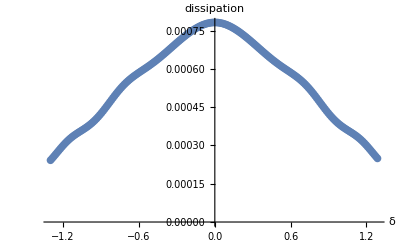

```mathematica
δDissipation={};
χ=10;β=χ^(2/3)-0.01;
δbegining=-1.3;δend=1.3;δnstep=200;
ProgressIndicator[Dynamic[(δ-δbegining)/(δend-δbegining)]]
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,
δDissipation=Append[δDissipation,{δ,GeneralLinearAnizatropy[10^-5,(β*χ^(-2/3))^2,χ,ArcSin[δ*χ^(-1/3)],π/2,{1,0.1}][[7]]}];
];
Clear[δ,β];

experiment=ListPlot[δDissipation,PlotRange->Full,AxesLabel->{δ,dissipation}];
result=Show[{experiment}]
```

```mathematica
ϕθDissipation={};
χ=30;β=χ^(2/3)-1;δ=0;
ϕbegining=0;ϕend=2π;ϕnstep=100;
θbegining =0; θend = 2π; θnstep = 100;
ProgressIndicator[Dynamic[(ϕ-ϕbegining)/(ϕend-ϕbegining)(*+((ϕend-ϕbegining)/ϕnstep)*(θ-θbegining)/(θend-θbegining)*)]]
For[ϕ=ϕbegining,ϕ<ϕend,ϕ+=(ϕend-ϕbegining)/ϕnstep,
For[θ=θbegining,θ<θend,θ+=(θend-θbegining)/θnstep,
sol=GeneralLinearAnizatropy[10^-5,(β*χ^(-2/3))^2,χ,ArcSin[δ*χ^(-1/3)],π/2,{Cos[θ],Sin[θ] ⅇ^(ⅈ ϕ)}];
ϕθDissipation=Append[ϕθDissipation,{Arg[sol[[4]][[2]]],ArcSin[Abs[sol[[4]][[2]]]],sol[[7]]}];
];
];
Clear[δ,β,ϕ,θ];

experiment=ListPlot3D[ϕθDissipation,PlotRange->Full,AxesLabel->{ϕ,θ,dissipation}];
result=Show[{experiment}]
```

-Graphics3D-

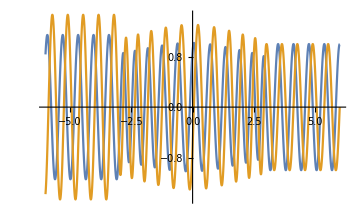
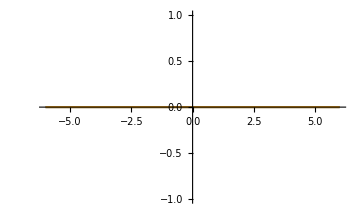
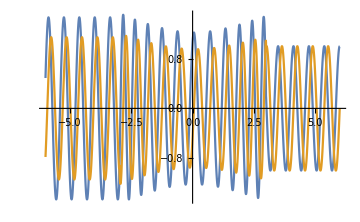
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

0.925479

```mathematica
χ=10;β=χ^(2/3)-0.01;δ=0;θ=π/2;ϕ=0;
sol=GeneralLinearAnizatropy[10^-3,(β*χ^(-2/3))^2,χ,ArcSin[δ*χ^(-1/3)],π/2,{Cos[θ],Sin[θ] ⅇ^(ⅈ ϕ)}];
Table[Plot[{Re[sol⟦3,i⟧[x]],Im[sol⟦3,i⟧[x]]},{x,-2X,2X},ImageSize->Medium],{i,1,4}]
sol[[7]]
```

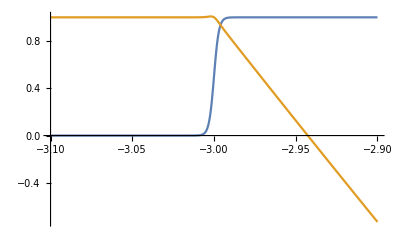

```mathematica
β=χ^(2/3)-0.1;
α=10^-5;(* - dissipation, α=ν/ω, ω->ω(1+ⅈα)*)
U=(β*χ^(-2/3))^2;(* - anizatropy: p^2=4πe^2*n/m, b=eB/(mc), v=p^2/ω^2, u=b^2/ω^2, and with dissipation: v->v(1-ⅈα), u->U(1-ⅈα)*)
(*χ - dimensionless wave vector magnitude; χ=Subscript[k, 0] L, and L=1*) 
(*θ - ngel between wave vector and XOZ*)
(*β - angle between wave vector and magnetic field direction*)
(*P - wave polarisation; 2d-vector*)

(*=====================================================================================================================*)

(*Plasma configuration*)
X=3;(*plasma boundary*)
Δ=0.001;(*smoothing width, in parts of plasma whight*)
n=1/Δ; smoothingFunc=Function[x,(1+(x/X)^(2n))^-1]; v=Function[x,((X^2-x^2)/(X^2-1))*smoothingFunc[x]*(1-ⅈ*α)]; u=U(1-ⅈ*α);
Eps=({{1-v[x]/(1-u), ⅈ(√u)/(1-u)v[x], 0}, {-ⅈ(√u)/(1-u)v[x], 1-v[x]/(1-u), 0}, {0, 0, 1-v[x]}}); 
Plot[{smoothingFunc[x],Re[Eps⟦1,1⟧]},{x,-X-0.1,-X+0.1}]
```

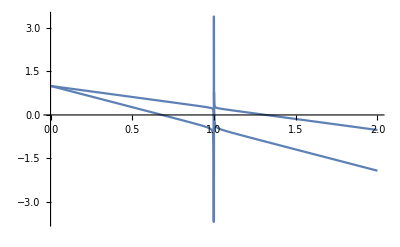

```mathematica
Plot[{1-(2x(1-x))/(2(1-x)(1+√y)-y δ^2),1-(2x(1-x))/(2(1-x)(1-√y)-y δ^2)}/.{y->0.1,δ->0.1},{x,0,2},PlotRange->Full]
```

```mathematica
DSolveValue[{D[V[x,y],x]==y ⅇ^((-x^2-y^2)/2),D[V[x,y],y]==-x ⅇ^((-x^2-y^2)/2)},V,{x,y}]
```

DSolveValue[{V^(1,0)[x,y]==ⅇ^(1/2 (-x^2-y^2)) y,V^(0,1)[x,y]==-ⅇ^(1/2 (-x^2-y^2)) x},V,{x,y}]